```mathematica
n=6;
knots=Table[i,{i,0,1,1/n}];
N0[x_]:=Table[Boole[knots[[i]]≤x<knots[[i+1]]],{i,1,n}]
```

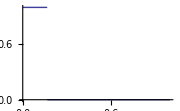
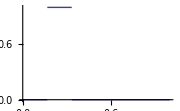
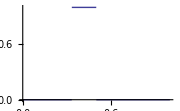
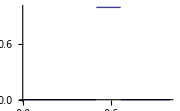
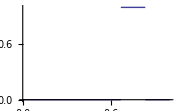
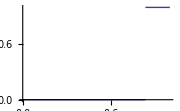

```mathematica
Table[Plot[N0[x][[i]],{x,0,1},ImageSize->Small],{i,1,n}]
```

```mathematica
N1[x_]:=Table[(x-knots[[i]])/(knots[[i+1]]-knots[[i]])N0[x][[i]]+(knots[[i+2]]-x)/(knots[[i+2]]-knots[[i+1]])N0[x][[i+1]],{i,1,n-1}]
```

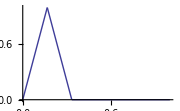
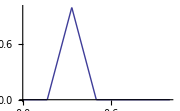
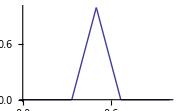
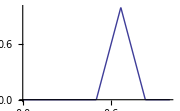
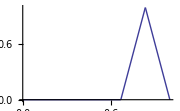

```mathematica
Table[Plot[N1[x][[i]],{x,0,1},PlotRange->{{0,1},{0,1}},ImageSize->Small],{i,1,n-1}]
```

```mathematica
N2[x_]:=Table[(x-knots[[i]])/(knots[[i+2]]-knots[[i]])N1[x][[i]]+(knots[[i+3]]-x)/(knots[[i+3]]-knots[[i+1]])N1[x][[i+1]],{i,1,n-2}]
```

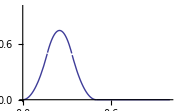
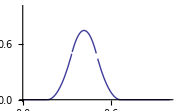
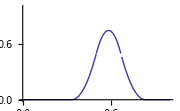
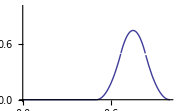

```mathematica
Table[Plot[N2[x][[i]],{x,0,1},PlotRange->{{0,1},{0,1}},ImageSize->Small],{i,1,n-2}]
```

```mathematica
N3[x_]:=Table[(x-knots[[i]])/(knots[[i+3]]-knots[[i]])N2[x][[i]]+(knots[[i+4]]-x)/(knots[[i+4]]-knots[[i+1]])N2[x][[i+1]],{i,1,n-3}]
```

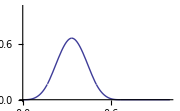
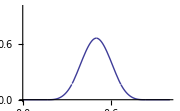
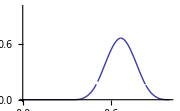

```mathematica
Table[Plot[N3[x][[i]],{x,0,1},PlotRange->{{0,1},{0,1}},ImageSize->Small],{i,1,n-3}]
```

```mathematica
Solve[{yi==Mi*dx^2*(1/6)+C*xi+D,yi2==Mi2*dx^2*(1/6)+C*xi2+D},D]
```

{}